```mathematica
Quit[];
```

```mathematica
$FeynCalcStartupMessages = False;
$LoadAddOns={"FeynArtsLoader"};
<<FeynCalc`
$FAVerbose = 0;
```

#### Write out all possible scalar products in COM frame

```mathematica
mw = SMP["m_W"];
p = Sqrt[En^2 -mw^2];
p1up = {En,0,0,p};
p1down = {En, 0, 0,-p};
p2up = {En, 0, 0, -p};
p2down = {En, 0, 0, p};
k1up = {En,p*Sin[θ],0,p*Cos[θ]};
k1down = {En,-p*Sin[θ],0,-p*Cos[θ]};
k2up = {En,-p*Sin[θ],0,-p*Cos[θ]};
k2down = {En,p*Sin[θ],0,p*Cos[θ]};
ep1up = 1/mw{p, 0, 0, En};
ep1down = 1/mw{p, 0, 0, -En};
ep2up = 1/mw{p, 0, 0, -En};
ep2down = 1/mw{p, 0, 0, En};
ek1up = 1/mw{p, En*Sin[θ], 0, En*Cos[θ]};
ek1down = 1/mw{p, -En*Sin[θ], 0, -En*Cos[θ]};
ek2up = 1/mw{p, -En*Sin[θ], 0, -En*Cos[θ]};
ek2down = 1/mw{p,En*Sin[θ], 0, En*Cos[θ]};
Rules = {Pair[Momentum[Polarization[p1,I]],Momentum[p1]] ->  ep1up.p1down,
Pair[Momentum[Polarization[p2,I]],Momentum[p2]] ->  ep2up.p2down,
 Pair[Momentum[Polarization[k2,-I]],Momentum[k2]] ->  ek2up.k2down,
 Pair[Momentum[Polarization[k1,-I]],Momentum[k1]]->  ek1up.k1down,
Pair[Momentum[Polarization[p1,I]],Momentum[p2]] ->  ep1up.p2down,
Pair[Momentum[Polarization[p1,I]],Momentum[k1]] ->  ep1up.k1down,
Pair[Momentum[Polarization[p1,I]],Momentum[k2]] ->  ep1up.k2down,
Pair[Momentum[Polarization[p2,I]],Momentum[p1]] ->  ep2up.p1down,
Pair[Momentum[Polarization[p2,I]],Momentum[k1]] ->  ep2up.k1down,
Pair[Momentum[Polarization[p2,I]],Momentum[k2]] ->  ep2up.k2down,
Pair[Momentum[Polarization[k1,-I]],Momentum[p1]] ->  ek1up.p1down,
Pair[Momentum[Polarization[k1,-I]],Momentum[p2]] ->  ek1up.p2down,
Pair[Momentum[Polarization[k1,-I]],Momentum[k2]] ->  ek1up.k2down,
Pair[Momentum[Polarization[k2,-I]],Momentum[p1]] ->  ek2up.p1down,
Pair[Momentum[Polarization[k2,-I]],Momentum[p2]] ->  ek2up.p2down,
Pair[Momentum[Polarization[k2,-I]],Momentum[k1]] ->  ek2up.k1down,
Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[p1,I]]] ->  ep1up.ep1down,Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[p2,I]]] ->  ep1up.ep2down,
Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[k1,-I]]] ->  ep1up.ek1down,
Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[k2,-I]]] ->  ep1up.ek2down,
Pair[Momentum[Polarization[p2,I]],Momentum[Polarization[p2,I]]] ->  ep2up.ep2down,
Pair[Momentum[Polarization[p2,I]],Momentum[Polarization[k1,-I]]] ->  ep2up.ek1down,
Pair[Momentum[Polarization[p2,I]],Momentum[Polarization[k2,-I]]] ->  ep2up.ek2down,
Pair[Momentum[Polarization[k1,-I]],Momentum[Polarization[k1,-I]]] ->  ek1up.ek1down,
Pair[Momentum[Polarization[k1,-I]],Momentum[Polarization[k2,-I]]] ->  ek1up.ek2down,
Pair[Momentum[Polarization[k2,-I]],Momentum[Polarization[k2,-I]]] ->  ek2up.ek2down};
SP[p1,p1] =p1up.p1down;
SP[p2,p2] =p2up.p2down;
SP[k1,k1] =k1up.k1down//Simplify;
SP[k2,k2] =k2up.k2down//Simplify;
SP[p1,p2] =p1up.p2down;
SP[p1,k1] =p1up.k1down;
SP[p1,k2] =p1up.k2down;
SP[p2,k1] =p2up.k1down;
SP[p2,k2] =p2up.k2down;
SP[k1,k2] =k1up.k2down//Simplify;
X = PolarizationVector[p1,μ]PolarizationVector[p2,ν]ComplexConjugate[PolarizationVector[k1,ρ]]ComplexConjugate[PolarizationVector[k2,σ]];
q = p1 - k1;
qs = p1 + p2;
```

#### 4 point amplitude

```mathematica
M1 = (-SMP["e"]^2)/SMP["sin_W"]^2(MT[μ,ν]MT[ρ,σ] + MT[μ,ρ]MT[ν,σ] - 2MT[μ,σ]MT[ν,ρ]);
M1amp =Contract[M1 X]/.Rules/.En-> Sqrt[S]/2;
M1ampS2 = Limit[M1amp/S^2,S->Infinity]//Simplify;
M1ampS1 = Limit[(M1amp - M1ampS2 *S*S)/S,S->Infinity]//Simplify;
M1ampS0 = Limit[M1amp - M1ampS2*S*S - M1ampS1*S,S->Infinity]//Simplify;
```

#### Higgs S channel

```mathematica
M2 = -SMP["e"]^2 mw^2/SMP["sin_W"]^2(MT[μ,ν]MT[ρ,σ])/(SP[(qs)] - SMP["m_H"]^2);
M2amp = Contract[M2 X]/.Rules/.En->Sqrt[S]/2;
M2ampS2 = Limit[M2amp/S^2,S->Infinity]//Simplify;
M2ampS1 = Limit[(M2amp - M2ampS2 *S*S)/S,S->Infinity]//Simplify;
M2ampS0 = Limit[M2amp - M2ampS2*S*S - M2ampS1*S,S->Infinity]//Simplify;
```

#### Higgs T channel

```mathematica
M3 = -SMP["e"]^2 mw^2/SMP["sin_W"]^2(MT[μ,ρ]MT[ν,σ])/(SP[(q)] - SMP["m_H"]^2);
M3amp = Contract[M3 X]/.Rules/.En->Sqrt[S]/2;
M3ampS2 = Limit[M3amp/S^2,S->Infinity]//Simplify;
M3ampS1 = Limit[(M3amp - M3ampS2 *S*S)/S,S->Infinity]//Simplify;
M3ampS0 = Limit[M3amp - M3ampS2*S*S - M3ampS1*S,S->Infinity]//Simplify;
```

#### γ/Z S channel

```mathematica
M4 = ( (SMP["e"]^2 MT[λ,κ])/ExpandScalarProduct[SP[(qs)]] + SMP["e"]^2 SMP["cos_W"]^2/SMP["sin_W"]^2(MT[λ,κ] - (FV[qs,λ]FV[qs,κ])/SMP["m_Z"]^2)/(ExpandScalarProduct[SP[(qs)]] - SMP["m_Z"]^2))(MT[α,β]FV[p1-p2,λ] + MT[β,λ]FV[p2 + qs,α] + MT[α,λ]FV[-qs -p1,β])(-(MT[μ,ν]FV[-k1+k2,κ] + MT[ν,κ]FV[-k2-qs,μ] + MT[μ,κ]FV[k1 + qs,ν]));
M4amp = ExpandScalarProduct[Contract[M4  PolarizationVector[p1,α]PolarizationVector[p2,β]ComplexConjugate[PolarizationVector[k1,μ]]ComplexConjugate[PolarizationVector[k2,ν]]]]/.Rules/.En->Sqrt[S]/2;
M4ampS2 = Limit[M4amp/S^2,S->Infinity]//Simplify;
M4ampS1 = Limit[(M4amp - M4ampS2 *S*S)/S,S->Infinity]//Simplify;
M4ampS0 = Limit[M4amp - M4ampS2*S*S - M4ampS1*S,S->Infinity]//Simplify;
```

#### γ/Z T channel

```mathematica
M5 = ( (SMP["e"]^2 MT[λ,κ])/ExpandScalarProduct[SP[(q)]] + SMP["e"]^2 SMP["cos_W"]^2/SMP["sin_W"]^2(MT[λ,κ] - (FV[q,λ]FV[q,κ])/SMP["m_Z"]^2)/(ExpandScalarProduct[SP[(q)]] - SMP["m_Z"]^2))(MT[α,μ]FV[p1+k1,λ] + MT[μ,λ]FV[-k1 + q,α] + MT[α,λ]FV[-q - p1,μ])(MT[β,ν]FV[-k2 - p2,κ] + MT[β,κ]FV[p2 -q,ν] + MT[ν,κ]FV[q+k2,β]);
M5amp = ExpandScalarProduct[Contract[M5  PolarizationVector[p1,α]PolarizationVector[p2,β]ComplexConjugate[PolarizationVector[k1,μ]]ComplexConjugate[PolarizationVector[k2,ν]]]]/.Rules/.En->Sqrt[S]/2//Simplify;
M5ampS2 = Limit[M5amp/S^2,S->Infinity]//Simplify;
M5ampS1 = Limit[(M5amp - M5ampS2 *S*S)/S,S->Infinity]//Simplify;
M5ampS0 = Limit[M5amp - M5ampS2*S*S - M5ampS1*S,S->Infinity]//Simplify;
```

#### Add up the S^2 and S^1 leading terms of the amplitude to verify correct high energy behavior

```mathematica
StringForm["(A^(S^2))^= ``", (M1ampS2 +M2ampS2 + M3ampS2 + M4ampS2 + M5ampS2)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//FullSimplify]
StringForm["(A^(S^1))^= ``", (M1ampS1 +M2ampS1 + M3ampS1 + M4ampS1 + M5ampS1)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//FullSimplify]
StringForm["(A^(S^0))^= ``", (M1ampS0 +M2ampS0 + M3ampS0 + M4ampS0 + M5ampS0)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//TrigExpand//FullSimplify]
```

(A^(S^2))^= 0

(A^(S^1))^= 0

(A^(S^0))^= (csc^2(2 θ_W) e^2 ((cos(2 θ)+7) csc^2(θ/2) m_W^2-8 cos^2(θ_W) m_H^2))/(4 m_W^2)

```mathematica
((M1ampS0 +M2ampS0 + M3ampS0 + M4ampS0 + M5ampS0)^2 - (M1ampS0 +SM2ampS0 + SM3ampS0 + M4ampS0 + M5ampS0)^2)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//TrigExpand//Simplify
```

(e^4 sin^2(α) (Mheavy^2-m_H^2) csc^4(θ_W) (-2 (cos(2 α)+3) m_H^2+(cos(2 θ)+7) csc^2(θ/2) m_W^2 sec^2(θ_W)-4 Mheavy^2 sin^2(α)))/(16 m_W^4)

#### Compute the cross section

```mathematica
Totalamp =( M1amp + M2amp + M3amp + M4amp + M5amp)/.SMP["e"]->SMP["g_W"]*SMP["sin_W"]/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2](SMP["m_W"])^2];
Totalampsquared = Totalamp*ComplexConjugate[Totalamp];
```

```mathematica
dsig[mh_]:= 1/(64 π^2*(S)^2)*Totalampsquared/.SMP["m_H"]->mh/.SMP["m_W"]-> 80.379/.SMP["cos_W"]->80.379/91.1876/.SMP["sin_W"]->Sqrt[1-(80.379/91.1876)^2]/.SMP["G_F"]-> 1.1663787*10^-5/.SMP["m_Z"]->91.1876;
```

```mathematica
lowSME = 10000;
highSME = 60000;
xs = Range[lowSME,highSME,500];
```

```mathematica
σsm[higgsmass_]:=Table[NIntegrate[(dsig[higgsmass]*2π*Sin[θ])/.S->SqrtS^2/.SqrtS->x ,{θ,0.0,π},Method->{Automatic,"SymbolicProcessing"->0}, MaxRecursion->100,PrecisionGoal->4,AccuracyGoal->4],{x,xs}];
```

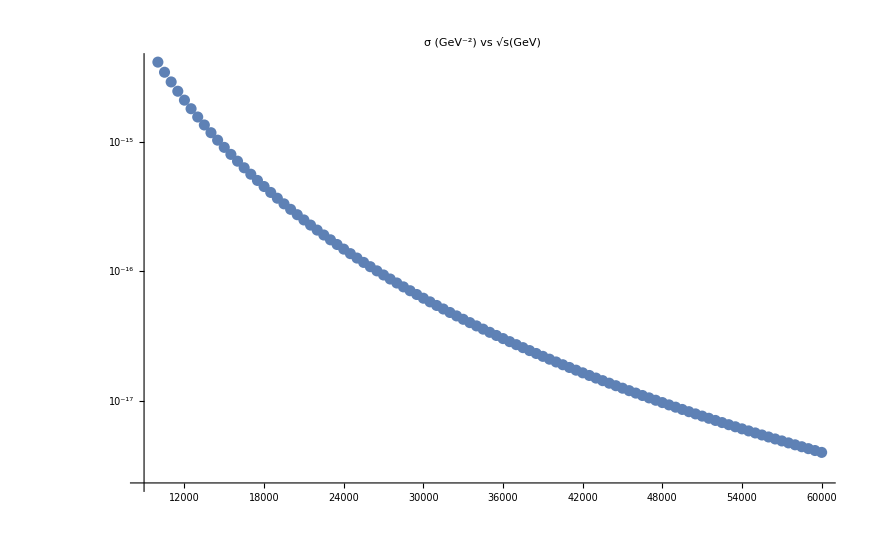

```mathematica
Subscript[σ, 125.1] = σsm[125.1];
data125 = Transpose@{xs,Subscript[σ, 125.1]};
s1 = ListLogPlot[data125, PlotLabel->"σ (GeV^-2) vs √s(GeV)",PlotRange->All];
Show[s1]
```

## Now we are going to add one singlet scalar

```mathematica
(*The only things that change are that we rescale Subscript[M, 125] couplings by cos(α) and introduce Subscript[M, Heavy] which has the same couplings but rescaled by sin(α)*)
```

#### Higgs S (New contribution from Heavy higgs and rescaled SM higgs coupling)

```mathematica
SM2 = -SMP["e"]^2 mw^2/SMP["sin_W"]^2(MT[μ,ν]MT[ρ,σ])/(SP[(qs)] - SMP["m_H"]^2)*(Cos[α])^2 + -SMP["e"]^2 mw^2/SMP["sin_W"]^2(MT[μ,ν]MT[ρ,σ])/(SP[(qs)] - (Mheavy)^2)*(Sin[α]^2);
SM2amp = Contract[SM2 X]/.Rules/.En->Sqrt[S]/2;
SM2ampS2 = Limit[SM2amp/S^2,S->Infinity]//Simplify;
SM2ampS1 = Limit[(SM2amp - SM2ampS2 *S*S)/S,S->Infinity]//Simplify;
SM2ampS0 = Limit[SM2amp - SM2ampS2*S*S - SM2ampS1*S,S->Infinity]//Simplify;
```

#### Higgs T channel (New contribution from Heavy higgs and rescaled SM higgs coupling)

```mathematica
SM3 = -SMP["e"]^2(Cos[α]^2)mw^2/SMP["sin_W"]^2(MT[μ,ρ]MT[ν,σ])/(SP[(q)] - SMP["m_H"]^2) + -SMP["e"]^2 Sin[α]^2 mw^2/SMP["sin_W"]^2(MT[μ,ρ]MT[ν,σ])/(SP[(q)] - (Mheavy)^2);
SM3amp = Contract[SM3 X]/.Rules/.En->Sqrt[S]/2;
SM3ampS2 = Limit[SM3amp/S^2,S->Infinity]//Simplify;
SM3ampS1 = Limit[(SM3amp - SM3ampS2 *S*S)/S,S->Infinity]//Simplify;
SM3ampS0 = Limit[SM3amp - SM3ampS2*S*S - SM3ampS1*S,S->Infinity]//Simplify;
```

#### Want to look at deviation from SM amplitude (A - A_SM)

```mathematica
δ = (SM2amp + SM3amp - M3amp - M2amp)/.SMP["e"]->SMP["g_W"]*SMP["sin_W"]/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2](SMP["m_W"])^2]/.Cos[α]->Sqrt[1 - Sin[α]^2]//Simplify
```

1/(√2)G_F ((cos^2(α) (4 m_W^2+S (cos(θ)-1))^2)/(2 m_H^2-(cos(θ)-1) (S-4 m_W^2))-(2 cos^2(α) (S-2 m_W^2)^2)/(S-m_H^2)+((4 m_W^2+S (cos(θ)-1))^2)/((cos(θ)-1) (S-4 m_W^2)-2 m_H^2)+(2 (S-2 m_W^2)^2)/(S-m_H^2)+(sin^2(α) (4 m_W^2+S (cos(θ)-1))^2)/(4 (cos(θ)-1) m_W^2+2 Mheavy^2-S cos(θ)+S)+(2 sin^2(α) (S-2 m_W^2)^2)/(Mheavy^2-S))

#### Let’s look at the S^2, S^1,S^0 behavior of the amplitude

```mathematica
StringForm["(A^(S^2))^= ``", (M1ampS2 +SM2ampS2 + SM3ampS2 + M4ampS2 + M5ampS2)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//FullSimplify]
StringForm["(A^(S^1))^= ``", (M1ampS1 +SM2ampS1 + SM3ampS1 + M4ampS1 + M5ampS1)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//FullSimplify]
StringForm["(A^(S^0))^= ``", (M1ampS0 +SM2ampS0 + SM3ampS0 + M4ampS0 + M5ampS0)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]]//FullSimplify]
```

(A^(S^2))^= 0

(A^(S^1))^= 0

(A^(S^0))^= (e^2 ((cos(2 θ)+7) csc^2(θ/2) csc^2(2 θ_W) m_W^2-2 csc^2(θ_W) (Mheavy^2 sin^2(α)+cos^2(α) m_H^2)))/(4 m_W^2)

```mathematica
(*So we see that A^(S^2)remains unmodified as well as A^(S^1)because the trig factors cancel,only A^(S^0)is modified at tree level. *)
```

#### Compute the cross section

```mathematica
STotalamp =( M1amp + SM2amp + SM3amp + M4amp + M5amp)/.SMP["e"]->SMP["g_W"]*SMP["sin_W"]/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2](SMP["m_W"])^2];
STotalampsquared = STotalamp*ComplexConjugate[STotalamp];
Sdsig = 1/(64 π^2*(S)^2)*STotalampsquared/.SMP["m_H"]->125.1/.SMP["m_W"]-> 80.379/.SMP["cos_W"]->80.379/91.1876/.SMP["sin_W"]->Sqrt[1-(80.379/91.1876)^2]/.SMP["G_F"]-> 1.1663787*10^-5/.SMP["m_Z"]->91.1876;
```

```mathematica
SquaredS2 = Limit[STotalampsquared/S^2/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]],S->Infinity]//Simplify;
```

```mathematica
SquaredS1 = Limit[(STotalampsquared - SquaredS2*S*S)/S/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]],S->Infinity]//Simplify;
```

```mathematica
SquaredS0 = Limit[(STotalampsquared - SquaredS2*S*S - SquaredS1*S )/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]],S->Infinity]//Simplify;
```

```mathematica
m1 = Plot[SquaredS0*Sin[θ]/.SMP["m_H"]->125.1/.SMP["m_W"]-> 80.379/.SMP["θ_W"]->80.379/91.1876/.SMP["θ_W"]->Sqrt[1-(80.379/91.1876)^2]/.SMP["G_F"]-> 1.1663787*10^-5/.SMP["m_Z"]->91.1876/.Sec[Subscript[θ, W]]-> 91.1876/80.379/.Mheavy->300/.α->π/4/.θ->x,{x,.1, π},PlotLegends->{"Mheavy = 300 GeV"},PlotStyle->Black];
m2= Plot[SquaredS0*Sin[θ]/.SMP["m_H"]->125.1/.SMP["m_W"]-> 80.379/.SMP["θ_W"]->80.379/91.1876/.SMP["θ_W"]->Sqrt[1-(80.379/91.1876)^2]/.SMP["G_F"]-> 1.1663787*10^-5/.SMP["m_Z"]->91.1876/.Sec[Subscript[θ, W]]-> 91.1876/80.379/.Mheavy->500/.α->π/4/.θ->x,{x,.1, π},PlotLegends->{"Mheavy = 500 GeV"},PlotStyle->Red];
m3= Plot[SquaredS0*Sin[θ]/.SMP["m_H"]->125.1/.SMP["m_W"]-> 80.379/.SMP["θ_W"]->80.379/91.1876/.SMP["θ_W"]->Sqrt[1-(80.379/91.1876)^2]/.SMP["G_F"]-> 1.1663787*10^-5/.SMP["m_Z"]->91.1876/.Sec[Subscript[θ, W]]-> 91.1876/80.379/.Mheavy->700/.α->π/4/.θ->x,{x,.1, π},PlotLegends->{"Mheavy = 700 GeV"},PlotStyle->Blue];
```

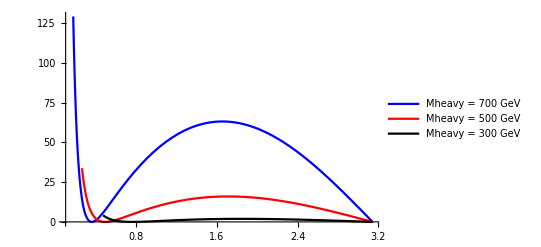

```mathematica
Show[m3,m2,m1]
```

```mathematica
lowE = 300;
highE = 10000;
xs = Range[lowE,highE,50];
```

```mathematica
σsing[sinα_,Mheav_]:=Table[NIntegrate[(Sdsig*2π*Sin[θ])/.Cos[α]->Sqrt[(1-Sin[α]^2)]/.S->SqrtS^2/.Sin[α]->sinα/.Mheavy->Mheav/.SqrtS->x ,{θ,0,π},Method->{Automatic,"SymbolicProcessing"->0}, MaxRecursion->100,PrecisionGoal->4,AccuracyGoal->4],{x,xs}];
```

```mathematica
(*σ_(.5) = σsing[.2,1500];
σ_(.2) = σsing[.1,1500];
σ_(.7) = σsing[.3,1500];*)
Subscript[σ, SM] = σsm[125.1];
```

```mathematica
data1= Transpose@{xs,σ_(.2) };
data2= Transpose@{xs,σ_(.5) };
data3= Transpose@{xs,σ_(.7)  };
data0= Transpose@{xs,Subscript[σ, SM]};
pl1 = ListPlot[data1, PlotLabel->"δσ/σ_SM vs √s (GeV) for M_Heavy = 1.5 TeV",PlotLegends->{"Sin[α] = 0.1"},PlotMarkers->{"o"},PlotStyle->Black];
pl2 = ListPlot[data2, PlotLabel->"δσ/σ_SM vs √s (GeV) for M_Heavy = 1.5 TeV",PlotLegends->{"Sin[α] = 0.2"},PlotMarkers->{"o"},PlotStyle->Red];
pl3 = ListPlot[data3, PlotLabel->"δσ/σ_SM vs √s (GeV) for M_Heavy = 1.5 TeV",PlotLegends->{"Sin[α] = 0.3"},PlotMarkers->{"o"},PlotStyle->Blue];
pl0 = ListPlot[data0, PlotLabel->"δσ/σ_SM vs E (GeV) for M_Heavy = 1 TeV",PlotLegends->{"SM"},PlotMarkers->{"o"},PlotStyle->Purple];

Show[pl3,pl2,pl1,pl0]
```

-Graphics-

```mathematica
sina = .1;m1 = 12000;m2 =14000;m3 = 16000;m4=18000;
Subscript[σ, 1] = σsing[sina,m1];
Subscript[σ, 2] = σsing[sina,m2];
Subscript[σ, 3] = σsing[sina,m3];
Subscript[σ, 4] = σsing[sina,m4];
```

```mathematica
data4= Transpose@{xs,Subscript[σ, 1]/Subscript[σ, SM]};
data5= Transpose@{xs,Subscript[σ, 2]/Subscript[σ, SM]};
data6= Transpose@{xs,Subscript[σ, 3]/Subscript[σ, SM] };
data7= Transpose@{xs,Subscript[σ, 4]/Subscript[σ, SM]};
pl4 = ListPlot[data4, PlotLabel->"σ_Singlet/σ_SM vs √s (GeV)",PlotLegends->{StringForm["Sin[α] = ``, M_Heavy = `` GeV",sina,m1]},PlotMarkers->{"o"},PlotStyle->Black,PlotRange->{.99,1.3}];
pl5 = ListPlot[data5, PlotLabel->"σ_Singlet/σ_SM vs √s (GeV)",PlotLegends->{StringForm["Sin[α] = ``, M_Heavy = `` GeV",sina,m2]},PlotMarkers->{"o"},PlotStyle->Red,PlotRange->{.99,1.3}];
pl6 = ListPlot[data6, PlotLabel->"σ_Singlet/σ_SM vs √s (GeV)",PlotLegends->{StringForm["Sin[α] = ``, M_Heavy = `` GeV",sina,m3]},PlotMarkers->{"o"},PlotStyle->Blue,PlotRange->{.99,1.3}];
pl7 = ListPlot[data7, PlotLabel->"σ_Singlet/σ_SM vs √s (GeV)",PlotLegends->{StringForm["Sin[α] = ``, M_Heavy = `` GeV",sina,m4]},PlotMarkers->{"o"},PlotStyle->Purple,PlotRange->{.99,1.3}];


Show[pl7,pl6,pl5,pl4]
```

-Graphics-

(A^(S^0))^= (csc^2(2 θ_W) e^2 ((cos(2 θ)+7) csc^2(θ/2) m_W^2-8 cos^2(θ_W) m_H^2))/(4 m_W^2)

```mathematica
Amp=1/(4 (1 - Subscript[m, w]^2/Subscript[m, z]^2)Subscript[m, w]^2/Subscript[m, z]^2 Subscript[m, w]^2)SMP["e"]^2((Cos[2θ] + 7)Csc[θ/2]^2 Subscript[m, w]^2 - 8 Subscript[m, w]^2/Subscript[m, z]^2 Subscript[m, h]^2)//Simplify
```

-(e^2 m_z^2 ((cos(2 θ)+7) csc^2(θ/2) m_z^2-8 m_h^2))/(4 m_w^2 (m_w^2-m_z^2))